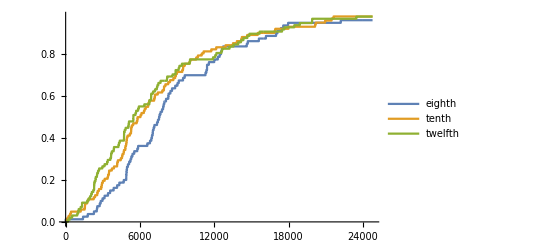

```mathematica
g8= ReadList["C:\\Users\\Ben Mirtchouk\\Desktop\\Computer Stuff\\C++\\moody\\facebook\\grade8.txt"][[1]];
g10= ReadList["C:\\Users\\Ben Mirtchouk\\Desktop\\Computer Stuff\\C++\\moody\\facebook\\grade10.txt"][[1]];
g12= ReadList["C:\\Users\\Ben Mirtchouk\\Desktop\\Computer Stuff\\C++\\moody\\facebook\\grade12.txt"][[1]];
ListLinePlot[{g8,g10,g12},PlotLegends->{"eighth","tenth","twelfth"}]
```

```mathematica
f[n_] := {g8[[n]], g10[[n]], g12[[n]]};
```

```mathematica
f[4900]
```

{0.225,0.372549,0.44898}

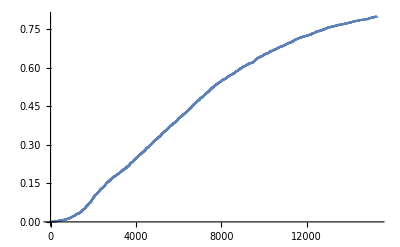

```mathematica
tot= ReadList["C:\\Users\\Ben Mirtchouk\\Desktop\\Computer Stuff\\C++\\moody\\facebook\\total.txt"][[1]];
ListLinePlot[tot,PlotLegends->"Total Vaping Prevalence"]
```

```mathematica
tot[[4900]]
```

0.317405

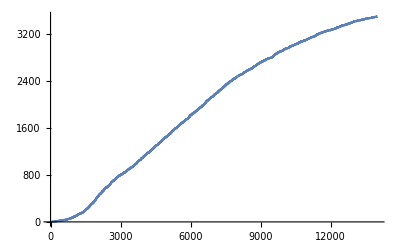

```mathematica
ListLinePlot[Table[tot[[i]]*4500 ,{i,1,14000}]]
```

```mathematica
14000/365.
```

38.3562